# 1. NALOGA: Aproksimacija števila π

Aproksimirana vrednost π: 3.128

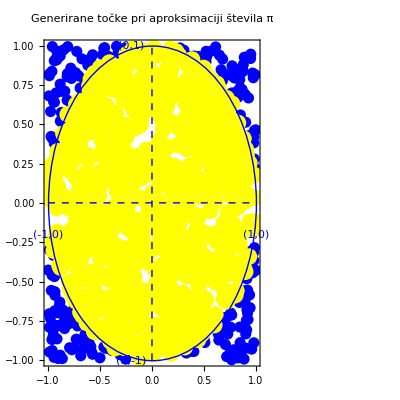

```mathematica
Get["C:\\Users\\vorsi\\Documents\\Faks\\Napredna računalniška orodja\\Wolfram Matehmatica\\Monaco.m"](*Spremeniti je potrebno pot na lokalno pot do datoteke na vašem računalniku, sicer koda ne bo delovala *)
result=montecarloPi[1000];

Print["Aproksimirana vrednost π: ",result[[1]]];
result[[2]]
```

# 2.)Aproksimacija funcije s taylorjevo vrsto

```mathematica
f[t_]=Sin[t] t^2 Exp[-t]
```

ⅇ^-t t^2 Sin[t]

```mathematica
n=5;(*Spremenite to vrednost glede na želeni red približka*)
taylor[t_]=Normal[Series[f[t],{t,2,n}]];
```

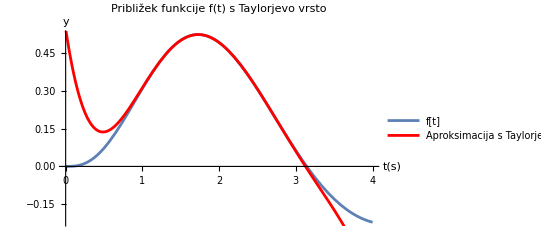

```mathematica
Show[Plot[f[t],{t,0,4},PlotLegends->{"f[t]"}],Plot[taylor[t],{t,0,4}, PlotStyle->Red,PlotLegends->{"Aproksimacija s Taylorjevo vrsto"}],AxesLabel->{HoldForm[t[s]],HoldForm[y]},PlotLabel->HoldForm["Približek funkcije f(t)  s Taylorjevo vrsto"],LabelStyle->{GrayLevel[0]}]
```

```mathematica
f[t_]=Sin[t] t^2 Exp[-t];
Manipulate[taylorApproximation[t_]=Normal[Series[f[t],{t,2,n}]];
Plot[{f[t],taylorApproximation[t]},{t,0,4},PlotRange->All,Epilog->{PointSize[Medium],Red,Point[{2,f[2]}]},PlotLegends->{"f(t)",Row[{"Približek ",HoldForm[Normal[Series[f[t],{t,2,n}]]]}]},AxesLabel->{"t","y"},PlotLabel->Row[{"Približek funkcije f(t) z redom ",n," v Taylorjevi vrsti"}]],{{n,2,"Red približka"},1,10,1,Appearance->"Labeled"}]
```